Nick G. Toth
Feb 5, 2020
Math 351
Assignment 4

Section 4.1

Exercise 1

x  |   0   |   2   |    3   |   4
----------------------------
y  |   7   |  11  |  28  |  63

g(x) = ∑_(i=0)^3 l_i(x)f(x_i)

l_0(x) = ∏ _(j=0
j≠0)^3 (x-x_j)/(0-x_j) = ((x-2)/(0-2)) ((x-3)/(0-3)) ((x-4)/(0-4))  = ((2-x)/2) ((3-x)/3) ((4-x)/4)=((2-x)(3-x)(4-x))/24 ,
l_1(x) =  ∏ _(j=0
j≠1)^3 (x-x_j)/(2-x_j) = ((x-0)/(2-0))((x-3)/(2-3))((x-4)/(2-4)) = (x/2) (3-x) ((4-x)/2)=(x(3-x)(4-x))/4 ,
l_2(x) =  ∏ _(j=0
j≠2)^3 (x-x_j)/(3-x_j) = ((x-0)/(3-0))((x-2)/(3-2))((x-4)/(3-4)) =(x/3) (x-2) (4-x)=(x(x-2) (4-x))/3 ,
l_3(x) =  ∏ _(j=0
j≠3)^3 (x-x_j)/(4-x_j) =((x-0)/(4-0))((x-2)/(4-2))((x-3)/(4-3)) = (x/4) ((x-2)/2) (x-3) = (x(x-2)(x-3))/8  .

So g(x) = ∑_(i=0)^3 l_i(x)f(x_i) = ((2-x)(3-x)(4-x))/24 f(x_0)+(x(3-x)(4-x))/4 f(x_1)+(x(x-2) (4-x))/3 f(x_2)+ (x(x-2)(x-3))/8 f(x_3)
                                                               =  7((2-x)(3-x)(4-x))/24+11(x(3-x)(4-x))/4+28(x(x-2) (4-x))/3+ 63(x(x-2)(x-3))/8

```mathematica
Factor[7((2-x)(3-x)(4-x))/24+11(x(3-x)(4-x))/4+28(x(x-2) (4-x))/3+ 63(x(x-2)(x-3))/8]
```

7-2 x+x^3

So g(x) = 7-2 x+x^3.

Now observe that g interpolates all of the points listed in the table.

```mathematica
g[x_]=7-2 x+x^3
Map[g, {0,2,3,4}]
```

{7,11,28,63}

Exercise 2

  x   |   y
-----------
  0   |    7
  2   |  11     (11-7)/(2-0)    =  2
  3   |  28     (28-11)/(3-2)  = 17     (17-2)/(3-0)   = 5     
  4   |  63     (63-28)/(4-3)  = 35     (35-17)/(4-2) = 9     (9-5)/(4-0) = 1

```mathematica
f[x_] = 7+2x+5x(x-2) + x(x-2) (x-3)
Map [f, {0,2,3,4}]
```

{7,11,28,63}

The polynomial obtained in this exercise is equivalent to the polynomial found in exercise 1, as we will show.

7 + 2x + 5x(x-2) + x(x-2) (x-3)  =  7+2x+5 x^2-10x+x^3-3 x^2-2 x^2+6x
                                                           =  7+x(2+6-10)+x^3+x^2(-3-2+5)
                                                           =  7-2x+x^3+0 x^2
                                                           =  x^3 -2x+7.

And, indeed, x^3 -2x+7 is the polynomial (g) obtained in exercise 1.

Exercise 3

For the four interpolation nodes −1,1,3,4, what are the l_i Functions(2) required in the Lagrange interpolation procedure? Draw the graphs of these four functions to show their essential properties.

l_0(x) = ∏ _(j=0
j≠0)^3 (x-x_j)/(0-x_j) = ((x-1)/(-1-1)) ((x-3)/(-1-3)) ((x-4)/(-1-4)) =((1-x)/2) ((3-x)/4) ((4-x)/5)=((1-x)(3-x)(4-x))/40 ,
l_1(x) =  ∏ _(j=0
j≠1)^3 (x-x_j)/(2-x_j) = ((x+1)/(1+1)) ((x-3)/(1-3)) ((x-4)/(1-4)) =((x+1)/2) ((3-x)/2) ((4-x)/3) = ((x+1)(3-x)(4-x))/12  ,
l_2(x) =  ∏ _(j=0
j≠2)^3 (x-x_j)/(3-x_j) = ((x+1)/(3+1))((x-1)/(3-1)) ((x-4)/(3-4)) =((x+1)/4)((x-1)/2) (4-x)=((x-1)(x+1)(4-x))/8=((x^2-1)(4-x))/8,
l_3(x) =  ∏ _(j=0
j≠3)^3 (x-x_j)/(4-x_j) =((x+1)/(4+1))((x-1)/(4-1)) ((x-3)/(4-3)) = ((x+1)/5)((x-1)/3) (x-3) = ((x-1)(x+1)(x-3))/15=((x^2-1)(x-3))/15 .

Observe the “essential properties” of {l_0, l_1, l_2, l_3}, by viewing the following graph.

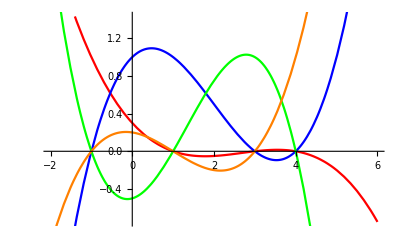

```mathematica
p1=Plot[((1-x)(3-x)(4-x))/40, {x,-2,6},PlotStyle->Red]
p2=Plot[((x+1)(3-x)(4-x))/12, {x,-2,6},PlotStyle->Blue]
p3=Plot[((x^2-1)(4-x))/8, {x,-2,6},PlotStyle->Green]
p4=Plot[((x^2-1)(x-3))/15 , {x,-2,6}, PlotStyle->Orange]
Show[p1,p2,p3,p4]
```

Perhaps the most essential of all the properties is the fact that all functions except for 1 are clearly equal to zero in certain spots (The nodes).
The next step, which we are skipping in this exercise, uses this property to solve for coefficients which make the sum of these functions equal to the given output-values at each of the nodes.

Exercise 4

We want to show that
p(1) = q(1) = 2
p(2) = q(2) = 1
p(3) = q(3) = 6
p(4) = q(4) = 47

```mathematica
p[x_]=5 x^3-27 x^2+45x-21
q[x_]=x^4-5 x^3+8 x^2-5x+3
Map [p, {1,2,3,4}]
Map [q, {1,2,3,4}]
```

{2,1,6,47}

{2,1,6,47}

So clearly both functions interpolate the points {(1,2), (2,1), (3,6), (4,47)}.

The uniqueness theorem is not violated because p is a degree 3 polynomial, and q is a degree 4 polynomial.
i.e. You can always transform a degree three polynomial into a degree four polynomial such that the two polynomials intersect in any four particular points.

Exercise 9

a)

x   |  0  |  1  |   2   |    4   |    6
---------------------------------
y   |  1  |  9  |  23  |  93  |  259

0  |  1	        	        
1  |  9	        	        (9-1)/(1-0)       =    8	        
2  |  23	        (23-9)/(2-1)     = 14	        (14-8)/(2-0)   = 3	        	        
4  |  93	        (93-23)/(4-2)   = 35	        (35-14)/(4-1) = 7	        	        (7-3)/(4-0)   =  1
6  |  259	        (259-93)/(6-4) = 83	        (83-35)/(6-2) = 12	        (12-7)/(6-1) = 1	        (1-1) = 0.

So f(x) = 1 + 8x + 3x(x-1)+ x(x-1)(x-2).
Observe that f interpolates the desired points:

```mathematica
f[x_]=1+8x+3x(x-1)+x(x-1)(x-2)
Map[f, {0,1,2,4,6}]
```

{1,9,23,93,259}

b) Now we want to evaluate f at 4.2.

```mathematica
f[4.2]
```

104.488

Exercise 11

From census data, the approximate population of the United States was 150.7 million in 1950, 179.3 million in 1960,
203.3 million in 1970, 226.5 million in 1980, and 249.6 million in 1990. Using Newton’s interpolation polynomial for
these data, find an approximate value for the population in 2000. Then use the polynomial to estimate the population
in 1920 based on these data. What conclusion should be drawn?

From the statement of the exercise, it is clear that we need to interpolate the points:
P = { (1950, 150.7), (1960, 179.3), (1970, 203.3), (1980, 226.5), (1990, 249.6) }

From this set we can form the divided difference table, as follows.

1950  |  150.7
1960  |  179.3     (179.3-150.7)/10 = 2.86     
1970  |  203.3     (203.3-179.3)/10 = 2.4       (2.4-2.86)/20 = -0.023
1980  |  226.5     (226.5-203.3)/10 = 2.32     (2.32-2.4)/20 = -0.004          (-0.004+0.023)/30 = 0.000633333
1990  |  249.6     (249.6-226.5)/10 = 2.31     (2.31-2.32)/20 = -0.0005     (-0.0005+0.004)/30 = 0.000116667     (0.000116667-0.000633333)/40 = -0.0000129167

Observe that the desired points are interpolated by the following polynomial.

```mathematica
f[x_] = 150.7+2.86(x-1950)-0.023 (x-1950)(x-1960) +0.000633333(x-1950)(x-1960)(x-1970) -0.0000129167(x-1950)(x-1960)(x-1970)(x-1980)

Map [f, {1950,1960,1970,1980,1990}]
```

{150.7,179.3,203.3,226.5,249.6}

Now we need to find an approximate value for the population in 2000.

```mathematica
f[2000]
```

270.2

Next we will use the polynomial to estimate the population in 1920.

```mathematica
f[1920]
```

-47.2001

What conclusion should be drawn?

I’m assuming the ‘conclusion’ is that interpolation involves approximation, and care should be taken to ensure that interpolated polynomials (in cases like this) be treated as approximations... i.e. It’s not as if the population was -47 million people in 1920.

Exercise 15

It is suspected that the following table comes from a cubic polynomial.

x   |  -2  |  -1  |   0   |    1   |   2   |    3
-----------------------------------------
y   |  1  |    4   |  11  |  16  |  13  |  -4

How can this be tested? Explain.

Construct the divided differences table
 x    |     y
-----------
-2    |    1
-1    |    4       (4-1)/(-1+2)   = 3
  0   |  11       (11-4)/(0+1)  = 7            (7-3)/(0+2)       =   2
  1   |  16       (16-11)/(1-0) = 5           (5-7)/(1+1)       =  -1       (-1-2)/(1+2)    = -1
  2   |  13       (13-16)/(2-1) = -3         (-3-5)/(2-0)       =  -4       (-4+1)/(2+1)   = -1       0
  3   |  -4       (-4-13)/(3-2)   = -17       (-17+3)/(3-1)   =  -7       (-7+4)/(3-0)    = -1       0        0

Now let f(x) = 1+3(x+2) + 2(x+2)(x+1) - x(x+2)(x+1), and observe that it interpolates the points in the given table.

```mathematica
f[x_]=1+3(x+2)+2(x+2)(x+1)-x(x+2)(x+1)
Map[f, {-2,-1,0,1,2,3}]
```

{1,4,11,16,13,-4}

Finally, the leading term of f is x(x+2)(x+1), which is clearly cubic, so f is cubic, and thus the table “comes from a cubic polynomial”.

Exercise 19

Let f (x) = x^3 + 2x^2 + x + 1.
a) Find the polynomial of degree 4 that interpolates the values of f at x = −2, −1, 0, 1, 2.

 x    |     y
-----------
-2    |    -1 
-1    |      1       (1+1)/(-1+2)  = 2
  0   |      1        (1-1)/(0+1)     = 0         (0-2)/(0+2)    = -1
  1   |      5        (5-1)/(1-0)      = 4         (4-0)/(1+1)    =   2       (2+1)/(1+2)  = 1
  2   |    19        (19-5)/(2-1)   = 14       (14-4)/(2-0)  =   5       (5-2)/(2+1)   = 1       (4/3-1)/(2+2)   = 0

So f(x) = -1 + 2(x+2) -(x+2)(x+1) + x(x+2)(x+1)

```mathematica
f[x_]=-1+2 (x+2)-(x+2) (x+1)+x(x+2)(x+1)
f/@{-2,-1,0,1,2}
```

{-1,1,1,5,19}

b) Find the polynomial of degree 2 that interpolates the values of f at x = −1,0,1.

 x    |     y
-----------
-1    |      1
  0   |      1        (1-1)/(0+1)     = 0
  1   |      5        (5-1)/(1-0)      = 4         (4-0)/(1+1)    = 2

```mathematica
f[x_]=1+2x(x+1)
f/@{-1,0,1}
```

{1,1,5}

Exercise 23

Form a divided-difference table for the following and explain what happened.

x |  1  |  2  |  3  |  1
---------------------
y |  3  |  5  |  5  |  7

You can’t interpolate this point set using polynomial interpolation. A function f:A->B is a subset of the Cartesian product of A and B with the property that for all x in A, there is a unique y in B such that f(x)  = y. In this case, we have f(1) = 3 and f(1) = 7, which means that the mapping is not unique. i.e. The table does not represent a function. We might as well have

  x   |      1      |    2   |   3
---------------------------
  y   |  (3, 7)  |   5    |   5

Creating a divided-difference table for this point-set is pointless (Ha).

On the other hand, perhaps we could produce a complex polynomial q with the property that
q(1+0i) = 3+7i
q(2+0i) = 5+0i
q(3+0i) = 5+0i

I’m going to try to create a divided difference table for this function. Maybe it will work, and maybe it won’t.

       z      |     q(z) 
---------------------
  1+0i     |     3+7i
  2+0i     |     5+0i          ((5+0i)-(3+7i))/((2+0i)-(1+0i)) = 2 - 7i
  3+0i     |     5+0i          0                                                                                (7i - 2)/((3+0i)-(1+0i) = (7i - 2)/2

Then q(z) = (3+7i) + (2 - 7i)(z-(1+0i)) + ((7i - 2)/2)(z-(1+0i))(z-(2+0i)) = 3+7i + (2 - 7i)(z-1) + ((7i - 2)/2)(z-1)(z-2)

q(1+0i) = q(1) = 3+7i + (2 - 7i)(1-1) + ((7i - 2)/2)(1-1)(1-2) = 3+7i
q(2+0i) = q(2) = 3+7i + (2 - 7i)(2-1) + ((7i - 2)/2)(2-1)(2-2) = 3+7i + 2 - 7i = 5 + 0i
q(3+0i) = q(3) = 3+7i + (2 - 7i)(3-1) + ((7i - 2)/2)(3-1)(3-2) = 3+7i + 4 - 14i + 7i - 2 = 5 + 0i.

Nice.

Now quaternions.
Jk.

Exercise 31

Use the uniqueness of the interpolating polynomial to verify that
 ∑_(i=0)^n f(x_i)l_i(x)= ∑_(i=0)^n f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j)

  Proof:
        By (3) on page 130, The newton interpolation polynomial can be written as  ∑_(i=0)^n a_i∏ _(j=0)^(i-1) (x-x_j).
        Therefore we must have  ∑_(i=0)^n a_i∏ _(j=0)^(i-1) (x-x_j)= ∑_(i=0)^n f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j), since the
        newton polynomial of degree n-1 is equivalent to the Lagrange polynomial of degree n-1 for the same
        set of n points.

        And  ∑_(i=0)^n a_i∏ _(j=0)^(i-1) (x-x_j)= ∑_(i=0)^n f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j) if and only if
        f[x_0,x_1,...,x_i] = a_i, since we would otherwise have different polynomials.
        
        Finally, by (7) on page 132, we have  a_k=  f[x_0,x_1,...,x_k] for all k, so we are done.
        QED.

Exercise 32

Show that the following explicit formula is valid for divided differences:
f[x_0,x_1,...,x_n]  =  ∑_(i=0)^n f(x_i)∏ _(j=0
j≠i)^n (x_i - x_j)^-1.

Be advised: The following is highly incomplete. This is just some of the work I did, but I’m a bit lost, and I need to get some sleep.

  Proof:
        From exercise 31, we have  ∑_(i=0)^n f(x_i)l_i(x)= ∑_(i=0)^n f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j).

         ∑_(i=0)^n f(x_i)l_i(x)= ∑_(i=0)^n f(x_i)∏ _(j=0
j≠i)^n ((x-x_j)/(x_i-x_j))= ∑_(i=0)^n f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j)
          So  ∑_(i=0)^n f(x_i)∏ _(j=0
j≠i)^n ((x-x_j)/(x_i-x_j))- ∑_(i=0)^n f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j)=0
         ∑_(i=0)^n (f(x_i)∏ _(j=0
j≠i)^n ((x-x_j)(x_i - x_j)^-1)-f[x_0,x_1,...,x_i]∏ _(j=0)^(i-1) (x-x_j) )=0

         Now f[x_0,x_1,...,x_i] = f(x_i)(∏ _(j=k+1)^n ((x-x_j)(x_i - x_j)^-1)-f[x_0,x_1,...,x_i]) 
        
        And our polynomial will be p_n(x)= ∑_(i=0)^n a_i∏ _(j=0)^(i-1) (x-x_j),
        Therefore a_i = f(x_i)∏ _(j=i+1)^n ((x-x_j)(x_i - x_j)^-1)-f[x_0,x_1,...,x_i] ,
         and since a_i = f[x_0,x_1,...,x_i], we have